```mathematica
f[x_]:=Exp[Sin[Cos[x]]]
```

```mathematica
Exp[Sin[Cos[x]]]
```

ⅇ^Sin[Cos[x]]

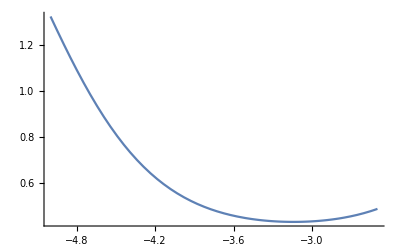

{0.431076,{x→-3.14159}}

```mathematica
Plot[f[x],{x,-5,-2.5}]
FindMinimum[f[x],{x,-5,-2.5}]
```

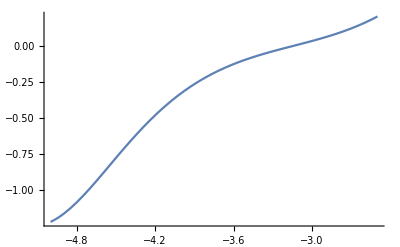

```mathematica
Plot[f'[x],{x,-5,-2.5}]
```

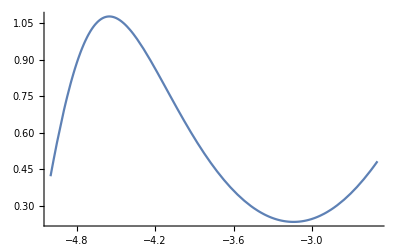

```mathematica
Plot[f''[x],{x,-5,-2.5}]
```

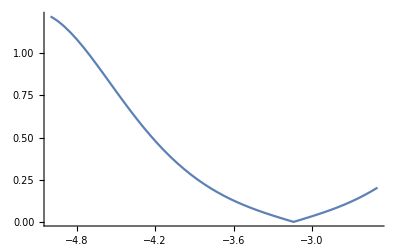

1.32296

```mathematica
Plot[Abs[f'[x]],{x,-5,-2.5}]
N[f[-5]]
```

```mathematica
f'[x]
f''[x]
```

-ⅇ^Sin[Cos[x]] Cos[Cos[x]] Sin[x]

-ⅇ^Sin[Cos[x]] Cos[x] Cos[Cos[x]]+ⅇ^Sin[Cos[x]] Cos[Cos[x]]^2 Sin[x]^2-ⅇ^Sin[Cos[x]] Sin[x]^2 Sin[Cos[x]]